# Scattering Kernels in 3D

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Gaussian

[Oblow et al. 1973 - effects of highly anisotropic scattering on monoenergetic neutron transport at deep penetrations] p.15:

```mathematica
pGaussian[u_,k_]:=Exp[-(u-1)^2/k]/((π^(3/2) Erf[2/(√k)])/(√(1/k)))
```

### Normalization condition

```mathematica
Integrate[2 Pi pGaussian[u,k],{u,-1,1},Assumptions->-1<k<1]
```

1

### Mean-cosine

```mathematica
Integrate[2 Pi pGaussian[u,k]u,{u,-1,1},Assumptions->k>0]
```

1+((-1+ⅇ^(-4/k)) √k)/(√π Erf[2/(√k)])

### Legendre expansion coefficients

```mathematica
Integrate[2 Pi (2k+1)pGaussian[Cos[y],e]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi},Assumptions->e>0]
```

1

```mathematica
Integrate[2 Pi (2k+1)pGaussian[Cos[y],e]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi},Assumptions->e>0]/.e->k
```

3+(3 (-1+ⅇ^(-4/k)) √k)/(√π Erf[2/(√k)])

```mathematica
Integrate[2 Pi (2k+1)pGaussian[Cos[y],e]LegendreP[k,Cos[y]]Sin[y]/.k->2,{y,0,Pi},Assumptions->e>0]/.e->k
```

5+(15 k)/4-(15 √k)/(√π Erf[2/(√k)])

```mathematica
Integrate[2 Pi (2k+1)pGaussian[Cos[y],e]LegendreP[k,Cos[y]]Sin[y]/.k->3,{y,0,Pi},Assumptions->e>0]/.e->k
```

7/4 (4+15 k+(2 ⅇ^(-4/k) √k (2+5 k-ⅇ^(4/k) (12+5 k)))/(√π Erf[2/(√k)]))

### sampling

```mathematica
cdf=Integrate[2 Pi pGaussian[u,k],{u,-1,x},Assumptions->0<x<1&&k>0]
```

1-Erf[(1-x)/(√k)]/Erf[2/(√k)]

```mathematica
Solve[cdf==xi,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1-√k InverseErf[-(-1+xi) Erf[2/(√k)]]}}

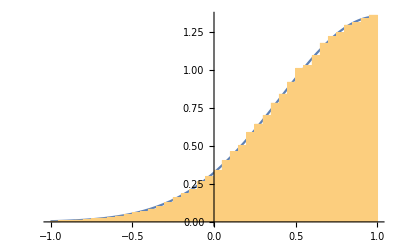

```mathematica
With[{k=.7},
Show[
Plot[2 Pi pGaussian[u,k],{u,-1,1}],
Histogram[Map[1-√k InverseErf[-(-1+#) Erf[2/(√k)]]&,Table[RandomReal[],{i,1,100000}]],50,"PDF"]
]
]
```